# Y-DNA 67 Marker RCC Calculations v7a

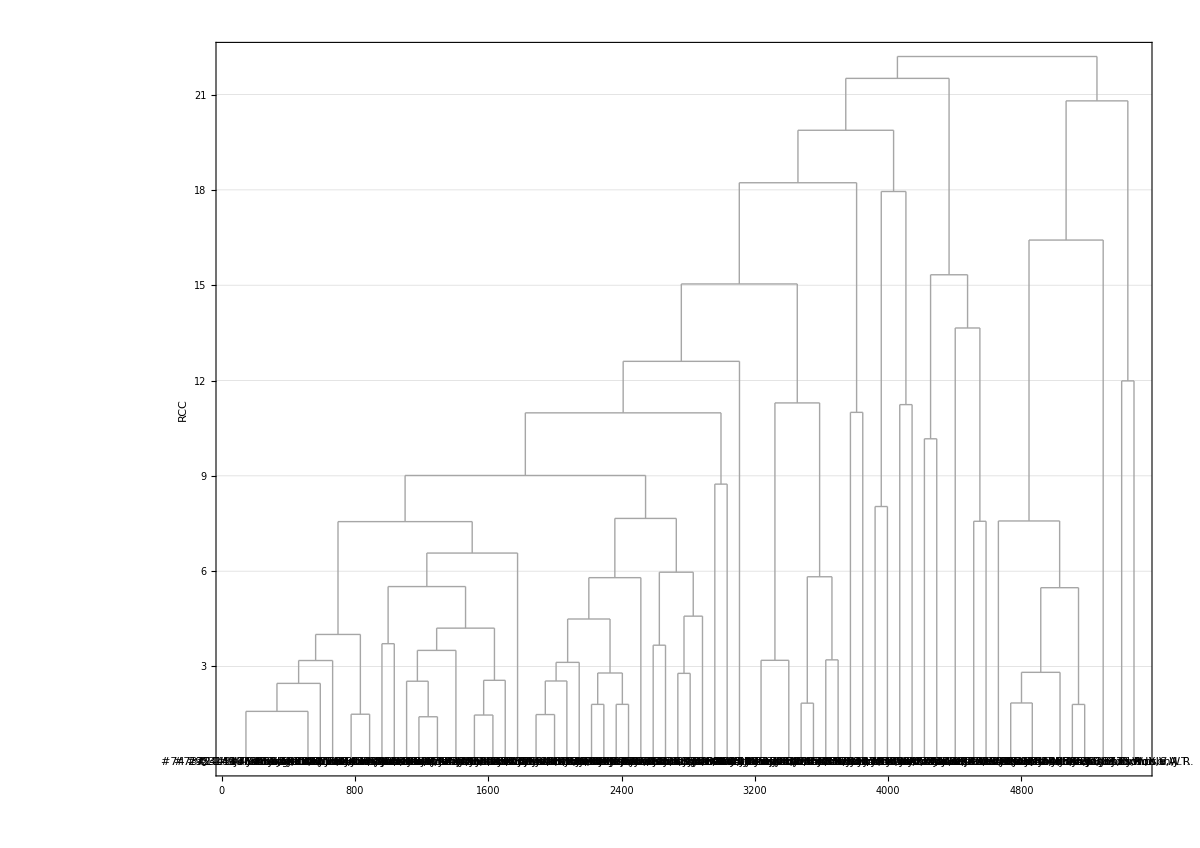

```mathematica
Needs["HierarchicalClustering`"]
fileset = "JOHNSTON - 67-Markers Data Set-v.7a";
csvin = "git/ydna-notebooks/jupyter/" <> fileset <> ".csv";
data = Delete[Import[csvin,"Data"],1];
data = Sort[data,#1[[1]] < #2[[1]] &]; (* sort in ascending order based on kit number *)
labels = Table[ToString[d[[1]]] <> " " <> d[[2]],{d,data}]; (* concatenate kit number and name for each kit into a list *)
labels = Reverse[Table[Rotate["#" <> ToString[i] <> " " <> labels[[i]],3Pi/2],{i,Length[labels]}]];
tests = Reverse[data[[All,Range[3,69]]]]; (* extract the Y-STR values for each kit into a 2D nested list with rows being kits and columns being Y-STR values *)
tree = ClusteringTree[tests->labels,ClusterDissimilarityFunction->"Average",DistanceFunction->((1/Correlation[#1,#2]-1)*10000&)];
Rotate[Dendrogram[tree
,Axes->{False,True}
, ImageSize->1200
, GridLines->{None,Automatic}
, Frame->{{True,True},{False,False}}
, GridLinesStyle -> Green
, FrameLabel -> {None,Rotate["RCC",Pi]}
],Pi/2]
```